# 第一章 概述

## 量子计算的基本概念

1.1 量子计算和量子信息简介

1.2 量子比特

1.3 量子计算

1.4 量子算法

1.5 量子信息处理（量子计算）实验

1.6 量子信息

## 1.1量子计算和量子信息简介

量子计算：利用量子系统及其特性完成信息处理任务

量子计算领域的远期目标是实现实用的通用量子计算，在某些问题的计算效率上超越任何经典计算机。将量子计算应用到基础物理、计算机、化学、生物、医学、金融等领域上。

基础物理：运用量子信息论的见解和技术，可以在量子引力(控制大质量物体的退相干)、量子场论和基础物理其他方面的理解方面取得重大进展。

量子系统的重要特性

态的线性叠加 (态和物理量的数学刻画)

概率性 (测量公理)

信息被储存在量子态中，但是以概率幅叠加的方式出现，不容易直接存取

纠缠和非定域性 (Bell test: 量子理论违背了定域实在性)

对环境敏感

小史

1930 能带结构计算首次用于预测新材料的特性

1956 约翰·巴丁 (John Bardeen)、莱昂·库珀 (Leon Cooper) 和约翰·施里弗 (John Schrieffer) 低温超导的BCS理论

1980 Klaus von Klitzing、Dorda 和 Pepper发现量子霍尔效应

1984 Charles Bennett 和 Gilles Brassard 将量子理论应用于密码协议，并证明量子密钥分发(QKD)可以增强信息安全性

1980s Richard Feynman：在量子计算机上模拟量子系统

1985 Deutsch 算法（oracle问题）

1994 Shor算法，多项式时间的因数分解算法。因数分解 ∈ BQP

1996  Grover 算法对非结构化搜索问题进行了量子加速

1996  Seth Lloyd ：以小时间步长演化可以有效模拟任何包含少粒子相互作用的多体量子哈密顿量； 模拟所需的总时间呈多项式增长。另一个链接

### 可计算性(computability)简介

数学、计算机科学、哲学(数理逻辑)

如何对数学中的算法进行抽象和严格定义？（图灵机）

计算机程序能够完成的任务的限度是什么？（computable function）有什么东西是超出限度的？（不可计算函数，停机问题等）

如何根据算法的复杂性进行分类？（复杂性类）

什么是证明？真命题都能够被证明吗？基于语义考虑的逻辑推论和基于形式推理考虑的定理的关系？

图灵机和可计算函数

-Graphics-

概率图灵机 (PTM) 两个转移函数，每步都等概率地使用其中一个。这个概念被用于定义 NP 问题和 BPP 问题。

记 𝐴^* 为 𝐴 能产生的所有字符串的集合

-Graphics-

函数的数量不可数多，图灵机可数多，一定存在一些不可计算的函数。

谓词(predicative)P 从A^*到{真，假}的函数。可计算的谓词是可判定的。

Turing-Church Thesis

数学上有严格定义的 computable partial function 正确的建立了 effectively calculable partial function 的概念。它本身并不是一个能够被证明的数学陈述。但人们可以寻找支持或反对丘奇论点的证据，有利的证据越多，这个论题就越合理。目前为止还没有反例。另外，独立构建的计算模型，比如 λ 演算和图灵机等最终都被证明是等价的。(令人惊讶的殊途同归)

就像函数的连续性的 𝛿 − 𝜖 定义一样，尽管可能和函数连续的直观理解在某种程度上有所出入，连续也已经被严格地数学化了，而且该定义非常有用。

### 计算复杂性类的简介

-Graphics-

-Graphics-

计算模型的层级(?)

在出现了概率性算法和量子计算以后，丘奇-图灵论题出现了一些变种。Ethan Bernstein 和 Umesh Vazirani 提出了经典复杂性理论丘奇-图灵论题：概率图灵机可以高效地模拟任何现实的计算模型。量子复杂性理论的丘奇-图灵论题：量子图灵机可以高效地模拟任何现实的计算模型。如果最终人们证明了 BPP 严格小于 BQP，也即量子计算在某些方面要比经典计算更加高效。那么经典复杂性理论丘奇-图灵论题将是错误的。当然，由于最原始的丘奇-图灵论题不涉及复杂性理论，只关注了函数的可计算性，所以其有效性不会受到影响。

计算模型之间有一个层级结构，可以简单地想成高级的模型能够高效地模拟低级模型的计算过程，反之则不能。我们想知道是否存在一个最高级的东西。基于信息是物理的这种想法，利用物理规律进行的计算或许就是最高级的。可能基于相对论、量子场论、大一统理论的计算模型能够比量子计算更高级。是否存在一种最终极的计算模型，它能够高效地模拟任何一种其他的计算模型？

### 超(越极)限的量子计算

量子计算的限度在哪里？我们如何超越这些极限？

## 1.2 量子比特

物理状态与物理量：经典vs量子

经典力学：某一时刻相空间中的点

经典电磁学：某一时刻空间中的电磁场电磁场分布

统计物理：系综的概率密度函数

经典信息(寄存器的状态)：{0,1}^n 中的一个字符串

量子力学/量子计算：态矢量、密度算符

共性?

-Graphics-

### 单比特

```mathematica
(*PacletInstall["https://www.wolframcloud.com/obj/wolframquantumframework/QuantumFramework.paclet",ForceVersionInstall->True]*)(*第一次运行时需要下载Paclet*)
```

```mathematica
<<Wolfram`QuantumFramework`(*每次重新启动Kernel都要导入Paclet*)
```

```mathematica
qubit=QuantumState[{α,β}];(*默认计算基，常用的ONB*)
qubit//TraditionalForm(*叠加态*)
qubit["Matrix"]//MatrixForm(*态矢量*)
m=((qubit["DensityMatrix"]//Normal)//FullSimplify)/.Conjugate[x_]:>SuperStar[x];
m//MatrixForm(*密度矩阵*)
Tr[m]//FullSimplify[#,Abs[α]^2+Abs[β]^2==1]&(*迹为1实际上是各个测量结果的概率归一*)
```

α 0+β 1

(α
β)

(Abs[α]^2 | α β^*
β α^* | Abs[β]^2)

1

#### qb的参数化与Bloch矢量

QuantumOperator[{"U3",θ,ω,-ω}]["Matrix"]//Normal//MatrixForm

(Cos[θ/2] | -ⅇ^(-ⅈ ω) Sin[θ/2]
ⅇ^(ⅈ ω) Sin[θ/2] | Cos[θ/2])

(Cos[θ/2] | -ⅇ^(-ⅈ ω) Sin[θ/2]
ⅇ^(ⅈ ω) Sin[θ/2] | Cos[θ/2])

```mathematica
qb=QuantumOperator[{"U3",θ,ϕ,-ϕ}][QuantumState[{1,0}]];
qb//TraditionalForm
```

Cos[θ/2] 0+ⅇ^(ⅈ ϕ) 1 Sin[θ/2]

```mathematica
Flatten[qb["Matrix"]]//Normal//MatrixForm
ρ=qb["DensityMatrix"]//Normal//Simplify[#,(ϕ|θ)∈Reals]&;
%//MatrixForm
Table[Tr[ρ.PauliMatrix[i]],{i,3}]//FullSimplify(*ω和ϕ分别是纬度角和经度角*)
```

(Cos[θ/2]
ⅇ^(ⅈ ϕ) Sin[θ/2])

(Cos[θ/2]^2 | 1/2 ⅇ^(-ⅈ ϕ) Sin[θ]
1/2 ⅇ^(ⅈ ϕ) Sin[θ] | Sin[θ/2]^2)

{Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ],Cos[θ]}

#### Bloch矢量的应用

思考：任意给定一个qubit的量子态ψ，如何找到U ∈ U(2)满足ψ = U|0⟩？
0绕着躺在x-y平面上的粉色轴(θ=π/2,ϕ)旋转蓝色角度ω 可以到达ψ
ψ  的Bloch矢量是{Cos[ϕ] Sin[ω],Sin[ω] Sin[ϕ],Cos[ω]}

```mathematica
Manipulate[mat=Chop[(MatrixExp[-I/2 ω Total[Table[PauliMatrix[i],{i,3}]CoordinateTransformData["Spherical"->"Cartesian","Mapping", {1,Pi/2,ϕ}]]])];GraphicsColumn[{Show[{ParametricPlot3D[Evaluate[m1=Chop[(MatrixExp[-I/2 ω1 Total[Table[PauliMatrix[i],{i,3}]CoordinateTransformData["Spherical"->"Cartesian","Mapping", {1,Pi/2,ϕ}]]])];
ρ=KroneckerProduct[m1.{1,0},Conjugate[m1.{1,0}]];
Table[Tr[ρ.PauliMatrix[i]],{i,3}]],{ω1,
0.001,ω}],QuantumState[mat.{1,0}]["BlochPlot"],Graphics3D[{Pink,Thick,Line[{CoordinateTransformData["Spherical"->"Cartesian","Mapping", {1.2,Pi/2,ϕ}],-CoordinateTransformData["Spherical"->"Cartesian","Mapping", {1.2,Pi/2,ϕ}]}]}]},Axes->False,PlotRange->All,AxesOrigin->{0,0,0}],TraditionalForm[QuantumState[QuantumState[mat.{1,0}]]]}],{{ω,1.7},0,Pi},{{ϕ,1.1},0,Pi}]
```

思考：还能找到其他转轴和转角实现目标吗？

#### 单比特测量

计算基下的测量

```mathematica
Manipulate[qb=QuantumState[{Cos[x],Sin[x]}];GraphicsColumn[{QuantumMeasurementOperator["Computational"][qb]["ProbabilityPlot"],"ψ = "TraditionalForm[qb]}],{{x,Pi/4},0,Pi/2}]
```

除了计算基以外的测量：测量σ_x

```mathematica
QuantumState[{α,β}]//TraditionalForm
q1=QuantumState[%,QuantumBasis[<|"+"->1/(√2){1,1},"-"->1/(√2){1,-1}|>]];
q1//TraditionalForm
```

α 0+β 1

(α/(√2)-β/(√2)) -+(α/(√2)+β/(√2)) +

```mathematica
N[QuantumMeasurementOperator["X"][q1]["Probabilities"]/.α->1/.β->0]//FullSimplify
```

<|x_+→0.5,x_−→0.5|>

### 多量子比特

#### 多比特的计算基

```mathematica
MatrixForm/@Flatten/@QuantumBasis[{2,2}]["Association"]
```

<|00→(1
0
0
0),01→(0
1
0
0),10→(0
0
1
0),11→(0
0
0
1)|>

```mathematica
Table[Symbol["a"<>ToString[i]<>ToString[j]],{i,0,1},{j,0,1}]
```

{{a00,a01},{a10,a11}}

```mathematica
qs2=QuantumState[{Subscript[a, "00"],Subscript[a, "01"],Subscript[a, "10"],Subscript[a, "11"]},QuantumBasis[{2,2}]];
%//TraditionalForm
```

00 a_00+01 a_01+10 a_10+11 a_11

```mathematica
QuantumMeasurementOperator["Computational",{1}][qs2];(*在计算基下测量第一个比特*)
#["Normalized"]&/@%["StateAssociation"]//TraditionalForm
```

<|0→(00 a_00)/(√(Abs[a_00]^2+Abs[a_01]^2))+(01 a_01)/(√(Abs[a_00]^2+Abs[a_01]^2)),1→(10 a_10)/(√(Abs[a_10]^2+Abs[a_11]^2))+(11 a_11)/(√(Abs[a_10]^2+Abs[a_11]^2))|>

```mathematica
#&/@QuantumMeasurementOperator["Computational",{1}][qs2]["Probabilities"]//FullSimplify[#,Conjugate[Subscript[a, "00"]] Subscript[a, "00"]+Conjugate[Subscript[a, "01"]] Subscript[a, "01"]+Conjugate[Subscript[a, "10"]] Subscript[a, "10"]+Conjugate[Subscript[a, "11"]] Subscript[a, "11"]==1]&//TraditionalForm
```

<|0→Re((a_00 Conjugate[(a_00)]+a_01 Conjugate[(a_01)])/(a_00 Conjugate[(a_00)]+a_01 Conjugate[(a_01)]+a_10 Conjugate[(a_10)]+a_11 Conjugate[(a_11)])),1→Re((a_10 Conjugate[(a_10)]+a_11 Conjugate[(a_11)])/(a_00 Conjugate[(a_00)]+a_01 Conjugate[(a_01)]+a_10 Conjugate[(a_10)]+a_11 Conjugate[(a_11)]))|>

Bell 基

```mathematica
QuantumState/@QuantumBasis["Bell"]["Association"]//TraditionalForm
```

<|Φ^+→00/(√2)+11/(√2),Φ^-→00/(√2)-11/(√2),Ψ^+→01/(√2)+10/(√2),Ψ^-→01/(√2)-10/(√2)|>

```mathematica
MatrixForm/@QuantumBasis["Bell"]["Association"]
```

<|Φ^+→(1/(√2)
0
0
1/(√2)),Φ^-→(1/(√2)
0
0
-1/(√2)),Ψ^+→(0
1/(√2)
1/(√2)
0),Ψ^-→(0
1/(√2)
-1/(√2)
0)|>

在计算基下测量Bell态，总是得到相同的结果

```mathematica
QuantumMeasurementOperator["Computational",{1}][QuantumState[{0,1,1,0}]]["StateAssociation"]//TraditionalForm
```

<|0→01,1→10|>

## 1.3 量子计算

-Graphics-

### 单比特门 U(2)

#### X 门 和 R_X(θ)门

```mathematica
opx=QuantumOperator["X"];
opx=QuantumOperator[PauliMatrix[1]];
opx["Matrix"]//Normal//MatrixForm
```

(0 | 1
1 | 0)

```mathematica
opx//TraditionalForm
```

01+10

```mathematica
(QuantumState/@(#/Norm[#]&/@Eigenvectors[PauliMatrix[1]]))//TraditionalForm
```

{-0/(√2)+1/(√2),0/(√2)+1/(√2)}

```mathematica
opx[QuantumState[{α,β}]]//TraditionalForm
```

β 0+α 1

```mathematica
QuantumOperator[{"RX",θ}]["Matrix"]//Normal//FullSimplify//MatrixForm
MatrixExp[-I θ/2 PauliMatrix[1]]//MatrixForm(*绕着x轴旋转角度θ*)
I %/.θ->Pi//MatrixForm
```

(Cos[θ/2] | -ⅈ Sin[θ/2]
-ⅈ Sin[θ/2] | Cos[θ/2])

(Cos[θ/2] | -ⅈ Sin[θ/2]
-ⅈ Sin[θ/2] | Cos[θ/2])

(0 | 1
1 | 0)

#### Y 门 和 R_Y(θ)门

```mathematica
opy=QuantumOperator[PauliMatrix[2]];
opy["Matrix"]//Normal//MatrixForm
```

(0 | -ⅈ
ⅈ | 0)

```mathematica
QuantumOperator[{"RY",θ}]["Matrix"]//Normal//FullSimplify//MatrixForm
MatrixExp[-I θ/2 PauliMatrix[2]]//MatrixForm
I %/.θ->Pi//MatrixForm
```

(Cos[θ/2] | -Sin[θ/2]
Sin[θ/2] | Cos[θ/2])

(Cos[θ/2] | -Sin[θ/2]
Sin[θ/2] | Cos[θ/2])

(0 | -ⅈ
ⅈ | 0)

#### Z 门 和 R_Z(θ)门

```mathematica
QuantumCircuitOperator["Z"];
%["Matrix"]//Normal//MatrixForm
```

(1 | 0
0 | -1)

```mathematica
QuantumOperator["Z"]//TraditionalForm
```

00-11

```mathematica
QuantumOperator[{"RZ",θ}]["Matrix"]//Normal//FullSimplify//MatrixForm
MatrixExp[-I θ/2 PauliMatrix[3]]//MatrixForm
I %/.θ->Pi//MatrixForm
```

(ⅇ^(-(ⅈ θ)/2) | 0
0 | ⅇ^((ⅈ θ)/2))

(ⅇ^(-(ⅈ θ)/2) | 0
0 | ⅇ^((ⅈ θ)/2))

(1 | 0
0 | -1)

#### 绕着轴 n=(x,y,z) 旋转角度 θ

```mathematica
n[i_]:={x,y,z}[[i]];
```

```mathematica
MatrixExp[-I θ/2 Sum[n[i] PauliMatrix[i],{i,3}]]//Simplify[#,{x,y,z}∈Sphere[]]&//FullSimplify//MatrixForm(*如何计算？习题4.4*)
```

(Cos[θ/2]-ⅈ z Sin[θ/2] | (-ⅈ x-y) Sin[θ/2]
(-ⅈ x+y) Sin[θ/2] | Cos[θ/2]+ⅈ z Sin[θ/2])

#### Hadamard 门

```mathematica
H=QuantumCircuitOperator["H"];
%["Matrix"]//Normal//MatrixForm
```

(1/(√2) | 1/(√2)
1/(√2) | -1/(√2))

```mathematica
QuantumOperator["H"]//TraditionalForm
QuantumOperator["H"]@QuantumState[{1,0}]//TraditionalForm
QuantumOperator["H"]@QuantumState[{0,1}]//TraditionalForm
```

00/(√2)+01/(√2)+10/(√2)-11/(√2)

0/(√2)+1/(√2)

0/(√2)-1/(√2)

```mathematica
(H/*H)["Matrix"]//Normal//MatrixForm
```

(1 | 0
0 | 1)

```mathematica
H[QuantumState[{1,0}]]//TraditionalForm
H[QuantumState[{0,1}]]//TraditionalForm
```

0/(√2)+1/(√2)

0/(√2)-1/(√2)

用 H 门制作均匀(等系数)叠加态

```mathematica
QuantumCircuitOperator["HHH"][QuantumState[{1,0,0,0,0,0,0,0}]]//TraditionalForm
```

000/(2 √2)+001/(2 √2)+010/(2 √2)+011/(2 √2)+100/(2 √2)+101/(2 √2)+110/(2 √2)+111/(2 √2)

#### 相位门 S

```mathematica
QuantumOperator["S"]["Matrix"]//Normal//MatrixForm
```

(1 | 0
0 | ⅈ)

#### T 门

```mathematica
QuantumOperator["T"]["Matrix"]//Normal//MatrixForm
```

(1 | 0
0 | ⅇ^((ⅈ π)/4))

#### 单比特门的 z-y-z 分解 旋量空间的欧拉角

```mathematica
zyz=E^(I α)QuantumOperator[{"RZ",β}]@QuantumOperator[{"RY",γ}]@QuantumOperator[{"RZ",δ}];
zyz["Matrix"]//Normal//MatrixForm//FullSimplify(*定理4.1*)
```

(1/2 ⅇ^(1/2 ⅈ (2 α-β-γ-δ)) (1+ⅇ^(ⅈ γ)) | 1/2 ⅈ ⅇ^(1/2 ⅈ (2 α-β-γ+δ)) (-1+ⅇ^(ⅈ γ))
-1/2 ⅈ ⅇ^(1/2 ⅈ (2 α+β-γ-δ)) (-1+ⅇ^(ⅈ γ)) | 1/2 ⅇ^(1/2 ⅈ (2 α+β-γ+δ)) (1+ⅇ^(ⅈ γ)))

```mathematica
Det[zyz["Matrix"]//Normal](*幺正与特殊幺正之间只相差相位角，半直积*)
```

ⅇ^(2 ⅈ α)

(SU (2)*U (1))/2 = U (2)

SU (2) 半直积 U (1) = U (2)

### 多比特量子门 U(2^n)

#### CNOT （controlled-NOT) 门

0000+0101+1011+1110

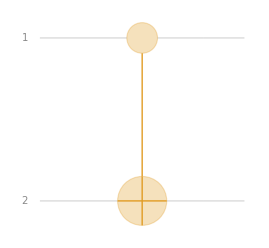

```mathematica
QuantumOperator["CNOT"]//TraditionalForm(*模2加法*)
QuantumCircuitOperator["CNOT"]//TraditionalForm
```

#### 交换门

0000+0110+1001+1111

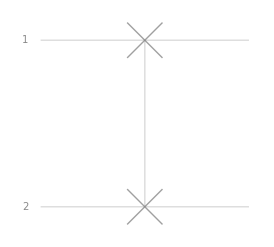

```mathematica
QuantumOperator["SWAP"]//TraditionalForm
QuantumCircuitOperator["SWAP"]//TraditionalForm
```

#### SWAP门拆成三个CNOT门

```mathematica
QuantumCircuitOperator[{QuantumOperator["CNOT",{1,2}],QuantumOperator["CNOT",{2,1}],QuantumOperator["CNOT",{1,2}]}]==QuantumCircuitOperator["SWAP"]
```

True

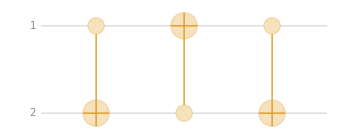

```mathematica
QuantumCircuitOperator[{QuantumOperator["CNOT",{1,2}],QuantumOperator["CNOT",{2,1}],QuantumOperator["CNOT",{1,2}]}]["Diagram"]
```

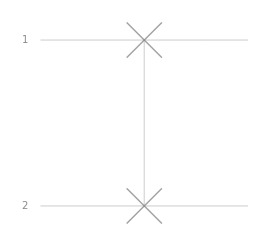

```mathematica
QuantumCircuitOperator["SWAP"]["Diagram"]
```

#### Toffoli 门 和 测量

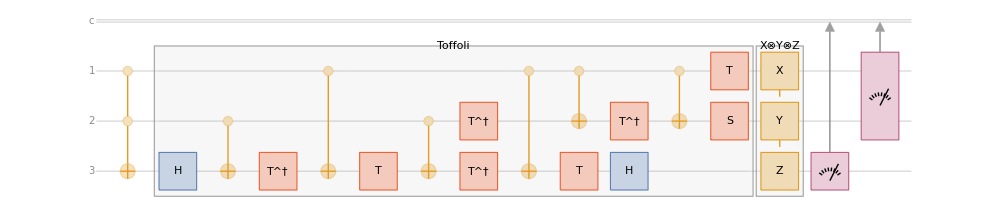

```mathematica
QuantumCircuitOperator[{QuantumOperator[…],QuantumCircuitOperator["Toffoli"],QuantumCircuitOperator[{"XYZ"}],QuantumMeasurementOperator["X",{3}],QuantumMeasurementOperator["X",{1,2}]}]["Diagram"]
```

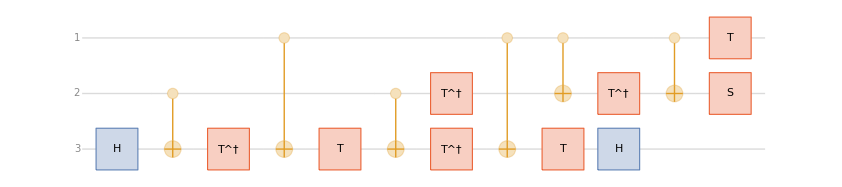

```mathematica
QuantumCircuitOperator["Toffoli"]["Diagram"]
```

```mathematica
tfl[a_,b_,c_]:={a,b,Mod[c+a b,2]}
```

```mathematica
QuantumOperator[…]["Matrix"]//Normal//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)

#### 量子线路

不出现回路，无环

不允许扇入扇出，扇入不可逆，扇出是量子克隆

### 通用门的集合

一组能够以任意的精度模拟任何量子幺正变换的门。

精度越高，需要的门越多。

### 从计算基中的态获得Bell 态

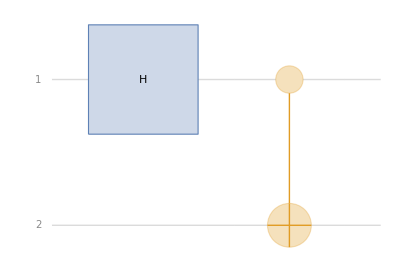

```mathematica
qco=QuantumCircuitOperator[{"H","CNOT"}];
qco["Diagram"]
```

```mathematica
TableForm[{QuantumBasis[{2,2}]["Names"],TraditionalForm/@qco/@(QuantumBasis[{2,2}]["PureStates"]),#["Formula"]&/@(QuantumState[#,QuantumBasis["Bell"]]&/@(qco/@(QuantumBasis[{2,2}]["PureStates"])))}//Transpose,TableHeadings->{{1,2,3,4},{"输入","输出"}}]
```

| 输入 | 输出 | 
1 | 00 | 00/(√2)+11/(√2) | Φ^+
2 | 01 | 01/(√2)+10/(√2) | Ψ^+
3 | 10 | 00/(√2)-11/(√2) | Φ^-
4 | 11 | 01/(√2)-10/(√2) | Ψ^-

### 利用Bell态进行隐形传态 (teleportation)

#### 方法1

设第1,2个比特是Alice的，而第3个比特是Bob的，双横线表示经典比特通信

```mathematica
ops={QuantumOperator["CX"],QuantumOperator["H"],QuantumOperator["CX",{2,3}],QuantumOperator["CZ",{1,3}],QuantumMeasurementOperator[],QuantumMeasurementOperator[{2}]};
```

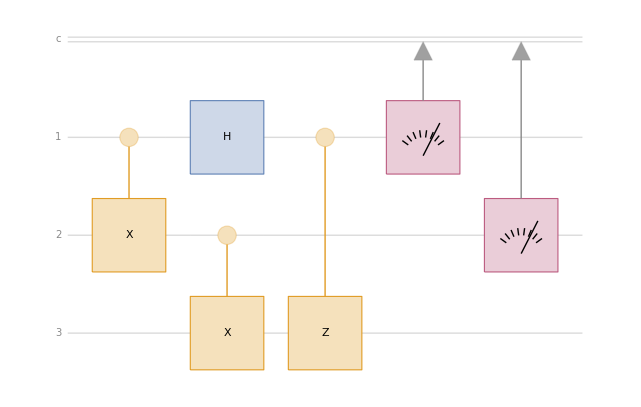

```mathematica
circuit=QuantumCircuitOperator[ops];
%["Diagram"]
```

```mathematica
QuantumCircuitOperator[{"CX","H","CX"->{2,3},"CZ"->{1,3},{1},{2}}]==circuit(*也可以用简写来构建线路*)
```

True

Alice的第一个比特ψ_0想要传给Bob，这个比特对Alice和Bob来说都是未知的，Alice的第二个比特和Bob的比特被制备在Bell态上

```mathematica
ψ0=QuantumTensorProduct[QuantumState[{α,β}],QuantumState["PhiPlus"]];
%["Formula"]
```

(α 000)/(√2)+(α 011)/(√2)+(β 100)/(√2)+(β 111)/(√2)

```mathematica
qss=circuit[ψ0]["StateAssociation"];
%//TraditionalForm
```

<|00→1/2 α 000+1/2 β 001,01→1/2 α 010+1/2 β 011,10→1/2 α 100+1/2 β 101,11→1/2 α 110+1/2 β 111|>

无论Alice的测量结果是什么，Bob手中的态都是ψ0

```mathematica
(QuantumPartialTrace[#,{1,2}]&/@qss)//TraditionalForm
```

<|00→1/4 α Conjugate[α] (00)+1/4 α Conjugate[β] (01)+1/4 β Conjugate[α] (10)+1/4 β Conjugate[β] (11),01→1/4 α Conjugate[α] (00)+1/4 α Conjugate[β] (01)+1/4 β Conjugate[α] (10)+1/4 β Conjugate[β] (11),10→1/4 α Conjugate[α] (00)+1/4 α Conjugate[β] (01)+1/4 β Conjugate[α] (10)+1/4 β Conjugate[β] (11),11→1/4 α Conjugate[α] (00)+1/4 α Conjugate[β] (01)+1/4 β Conjugate[α] (10)+1/4 β Conjugate[β] (11)|>

#### 方法2：LOCC ( local operations and classical communication )

Alice在本地执行一系列的逻辑门和测量，将测量结果告诉Bob

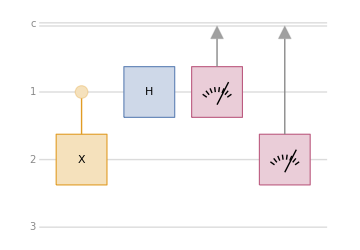

```mathematica
qco2=QuantumCircuitOperator[{"I"->3,{"CX"},"H",{1},{2}}];
qco2["Diagram"]
```

Bob根据Alice的测量结果对自己的态作用逻辑门以得到正确的ψ0

```mathematica
qss2=qco2[ψ0]["StateAssociation"];(*没有正确的归一化*)
%//TraditionalForm
```

<|00→1/2 α 000+1/2 β 001,01→1/2 β 010+1/2 α 011,10→1/2 α 100-1/2 β 101,11→-1/2 β 110+1/2 α 111|>

```mathematica
QuantumOperator["X",3]@qss2[[2]]//TraditionalForm
-QuantumOperator["Z",3]@qss2[[3]]//TraditionalForm
-QuantumOperator["X",3]@QuantumOperator["Z",3]@qss2[[4]]//TraditionalForm
```

1/2 α 100+1/2 β 101

1/2 α 100+1/2 β 101

1/2 α 000+1/2 β 001

信息的传递就是物质的传递

## 1.4 量子算法

### 量子计算机上的经典计算

Landauer原理

Information is physical (Landauer, 1991).

-Graphics-

不可逆的经典逻辑门都可以等效地用可逆的量子门替代。

曲面z = f(x,y)可能不是单射，但是graph of a function (x, y, z(x,y))  是单射

用量子测量的概率性模拟概率经典计算机

经典Toffoli门

```mathematica
tfl[a_,b_,c_]:={a,b,Mod[c+a b,2]}
```

```mathematica
Flatten[Table[{a,b,c},{a,0,1},{b,0,1},{c,0,1}],2]
tfl@@@%
tfl@@@%(*连续作用两次回到原来的值*)
```

{{0,0,0},{0,0,1},{0,1,0},{0,1,1},{1,0,0},{1,0,1},{1,1,0},{1,1,1}}

{{0,0,0},{0,0,1},{0,1,0},{0,1,1},{1,0,0},{1,0,1},{1,1,1},{1,1,0}}

{{0,0,0},{0,0,1},{0,1,0},{0,1,1},{1,0,0},{1,0,1},{1,1,0},{1,1,1}}

### 量子并行

量子计算机能同时（在同一个幺正变换中）计算函数f(x)在许多x处的值

### Deutsch 算法 f : {0,1}{0,1}

#### 平衡型函数 f (x) = x 或者 f(x)=x1

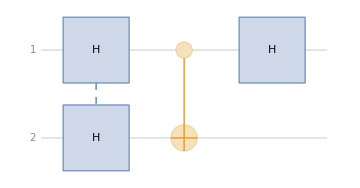

```mathematica
qc1 = QuantumCircuitOperator[{"H"->{1,2},"CNOT","H"}];(*设f(x) = x*)
qc1["Diagram"]
QuantumCircuitMultiwayGraph[qc1];
```

```mathematica
steps=ComposeList[qc1["Operators"],QuantumState[{0,1,0,0}]];
```

```mathematica
Grid[Transpose[{Style[#,Bold]&/@{"初态","经过前两个H门","(:7ecf:8fc7U)_f","经过最后的H门"},#["Formula"]&/@steps⟦;;⟧}],Frame->All,Alignment->Left]
```

初态 | 01
经过前两个H门 | 00/2-01/2+10/2-11/2
经过U_f | 00/2-01/2-10/2+11/2
经过最后的H门 | 10/(√2)-11/(√2)

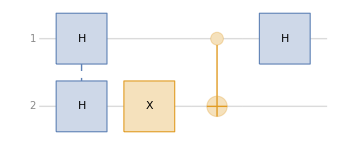

-10/(√2)+11/(√2)

```mathematica
qc2 = QuantumCircuitOperator[{"H"->{1,2},"X"->2,"CNOT","H"}];(*f(x)=x1*)
qc2["Diagram"]
qc2[QuantumState[{0,1,0,0}]]["Formula"]
```

#### 常数型函数 f(x)=1或 f(x)=0

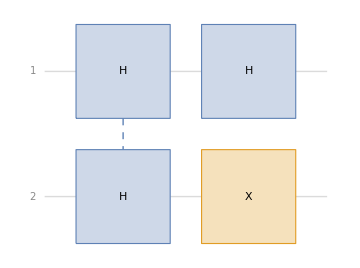

-00/(√2)+01/(√2)

```mathematica
qc3 = QuantumCircuitOperator[{"H"->{1,2},"X"->2,"H"}];(*f(x)=1*)
qc3["Diagram"]
qc3[QuantumState[{0,1,0,0}]]["Formula"]
```

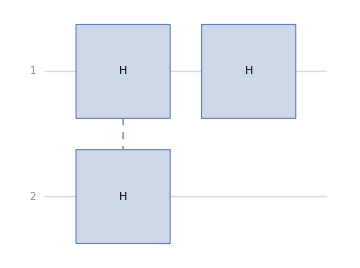

00/(√2)-01/(√2)

```mathematica
qc4 = QuantumCircuitOperator[{"H"->{1,2},"H"}];(*f(x)=1*)
qc4["Diagram"]
qc4[QuantumState[{0,1,0,0}]]["Formula"]
```

根据第一个qubit的测量结果，我们就能知道函数是平衡型还是常数型，也即计算了f(0)f(1)的值，对于常数型f(0)f(1)=0，对于平衡型f(0)f(1)=1

每个量子线路都只使用了一次U_f，即只需要一次计算就完成了经典计算需要两次计算才能完成的任务

启发：对于那些经典计算获得的信息量超过问题的答案能够提供的信息量的问题（尝试计算信息量），也即经典计算存在计算冗余的问题，量子计算具有潜在的加速可能

判断平衡型和常数型的量子算法推广到 f 具有 n 个slot的情况，称为Deutsch-Jozsa算法，参见 Sec.1.4.4

### 量子算法的总结

基于量子Fourier变换的方法

1/(√n)∑_(r=1)^n u_r e^(2π i(r-1)(s-1)/n) ,s =1,..,n

量子傅里叶变换能提供指数加速，但是傅里叶变换的结果被保存在振幅中，需要巧妙地提取

应用：Shor算法、Deutsch-Jozsa算法、隐藏子群问题。

量子搜索算法 经典O(N/2) 量子O(N)

量子模拟

量子计算的威力：BQP是严格大于BPP？但愿存在某些问题是量子计算机的概率算法能高效解决，但是概率图灵机不能高效解决的

## 1.5 量子信息处理（量子计算）实验

### Stern-Gerlach

对于级联的ZXZ测量，量子力学正确地解释了实验结果

### 前景

阈值定理，如果量子噪声水平降低到某个阈值以下，就能在工程上真正实现任意规模的量子计算。

状态层析和量子层析

小规模：量子通信

中等规模（Noisy Intermediate Scale Quantum (NISQ)）量子计算

大规模

被用于量子计算的物理系统：1. 光学系统；2. 超导线路；3. 离子阱；4. 冷原子；5. NV 色心；6. 核磁共振；7.任意子；8.transmon

### 多少比特了？

IBM Quantum

量子本源

...

## 1.6 量子信息

### 经典信息论

两个基本问题：

数据压缩的极限是什么？答：熵 H

数据传输速率的极限是什么？答：信道容量 C

### 量子信息论

狭义的量子信息：量子领域中和经典信息对应的理论。

量子信息的基本目标

确定量子力学静态资源的基本类型（资源理论）

确定量子力学动态过程的基本类型（量子信道）

量化基本动态过程导致的资源的取舍。例如，回答问题：为了在噪声信道中可靠地传递消息，至少需要多少资源？

lorem ipsum dolor sit amet, consectetuer adipiscing elit, sed diam nonummy.
		Lorem Ipsum